# Coauthor Network Analysis: Investigation into Endnote Bibliographic Data

## Wang Chengjun

## 20110507@HALL 8

http : // mathgis.blogspot.com/2010/04/play - with - bibliographic - data.html

## Data Clean

### Imort xml data

```mathematica
xml=Import["D:/Jonathan's COM8005/IMC/pr and mc.xml"];  (*note: in this way, you can add your annotation*)
```

### Get authors information

```mathematica
authors=Cases[xml,XMLElement["authors",_,authors_]->authors,Infinity];
```

```mathematica
names=Flatten@Cases[#,XMLElement["author",_,{XMLElement["style",_,names_]}]->names]&/@authors;
```

```mathematica
names
```

{{Austin, L. L.},{Avidar, R.},{Beebe, A.,Blaylock, A.,Sweetser, K. D.},{Callison, C.,Seltzer, T.},{Chen, N.},{Curtis, L.,Edwards, C.,Fraser, K. L.,Gudelsky, S.,Holmquist, J.,Thornton, K.,Sweetser, K. D.},{Diga, M.,Kelleher, T.},{DiStaso, M. W.,Stacks, D. W.,Botan, C. H.},{Erzikova, E.},{Eyrich, N.,Padman, M. L.,Sweetser, K. D.},{Girona, R.,Xifra, J.},{Han, G.,Zhang, A.},{Kim, S.,Park, J. H.,Wertz, E. K.},{Kitchen, P. J.,Panopoulos, A.},{Lariscy, R. W.,Avery, E. J.,Sweetser, K. D.,Howes, P.},{Lee, H.,Park, S. A.,Lee, Y.,Cameron, G. T.},{Lee, M.},{Lee, S.,Yoon, Y.},{Li, C. X.,Cropp, F.,Jin, Y.},{McAllister-Spooner, S. M.},{McCorkindale, T.},{O'Connor, A.,Shumate, M.,Meister, M.},{Pan, P. L.,Xu, J.},{Park, H.,Reber, B. H.},{Rybalko, S.,Seltzer, T.},{Searson, E. M.,Johnson, M. A.},{Seo, H.,Kim, J. Y.,Yang, S. U.},{Smith, B. G.},{Taylor, M.},{Toledano, M.},{Wang, J.,Chaudhri, V.},{Waters, R. D.,Burnett, E.,Lamm, A.,Lucas, J.},{Wigley, S.,Fontenot, M.},{Yang, A. M.,Taylor, M.},{Zhang, A.,Shen, H. M.,Jiang, H.},{Zoch, L. M.,Collins, E. L.,Sisco, H. F.,Supa, D. H.},{Aldoory, L.,Kim, J. N.,Tindall, N.},{Beurer-Zuellig, B.,Fieseler, C.,Meckel, M.},{Bowen, S. A.},{Brunner, B. R.,Huber, L. R. B.},{Choi, Y.,Lin, Y. H.},{Coombs, W. T.,Holladay, S. J.},{Daymon, C.,Hodges, C.},{Edwards, L.},{Han, E.,Ki, E. J.},{Hong, S. Y.,Yang, S. U.,Rim, H.},{Huertas, A.},{Hung, C. J. F.,Chen, Y. R. R.},{Hwang, S.},{Jaques, T.},{Jeffrey, L.,Brunton, M.},{Jeong, S. H.},{Jin, Y.},{Jin, Y.,Hong, S. Y.},{Kim, J. R.,Kim, J. N.},{Kim, S. Y.,Reber, B. H.},{Kiousis, S.,Stromback, J.},{Li, H. M.,Tang, L.},{Lim, J.,Jones, L.},{Luoma-Aho, V.,Vos, M.},{Luque-Martinez, T.,Del Barrio-Garcia, S.},{Miller, A. N.,Littlefield, R. S.},{Porter, L.},{Russell, K. M.,Bishop, C. O.},{Sweetser, K. D.,Brown, C. W.},{Tindall, N. T. J.},{Veil, S. R.},{Veil, S. R.,Rodgers, J. E.},{White, C.,Park, J.},{Witmer, D. F.,Silverman, D. A.,Gaschen, D. J.},{Zhang, E.,Benoit, W. L.},{Zhang, J. Y.,Swartz, B. C.}}

### Caculate the distribution

```mathematica
table=Sort[Tally[Length[#]&/@names],#1[[1]]<#2[[1]]&];
```

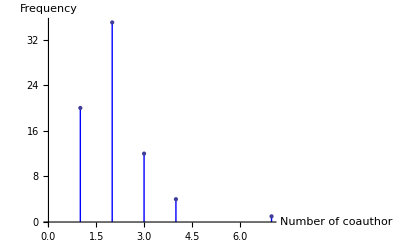

```mathematica
ListPlot[table,Filling->Axis,FillingStyle->Blue,AxesLabel->{"Number of coauthor","Frequency"}]
```

## Author Participation

### Split the coauthors

```mathematica
split=SplitBy[#,".,"]&/@Sort[names];
```

### Permutations of co-author

```mathematica
Permutations[#,{2}]&/@split;
```

### Select single author

```mathematica
single=Select[#,Length[#]<=1&]&/@split;
```

```mathematica
[[#]:>[#,#]]&/@single
```

```mathematica
data=If[Length[#]>1,Permutations[#,{2}],Length[#]<=1, {{{#_}}:>{{#_,#_}}}]&/@split;
(*however, if the length is smaller than 2 it will be blank*)
```

## GraphPlot

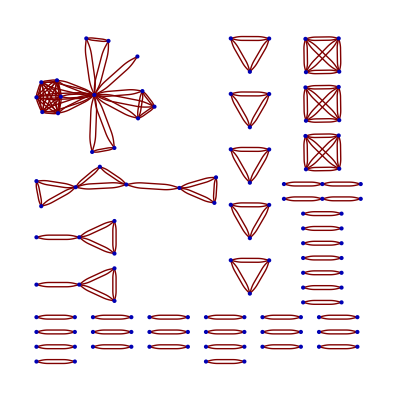

```mathematica
GraphPlot[Flatten[Flatten[Permutations[#,{2}]&/@split,1]/.{x_,y_}:>{x->y}]]
```

### Visualizing Retweeting Relationship

```mathematica
v=Import["C:\Python2.7\chengjun's python syntax\out/victoria.csv"];
```

```mathematica
split=Flatten[Flatten[SplitBy[#,".,"]&/@Sort[v]/.{x_,y_}:>{x->y},3]];
```

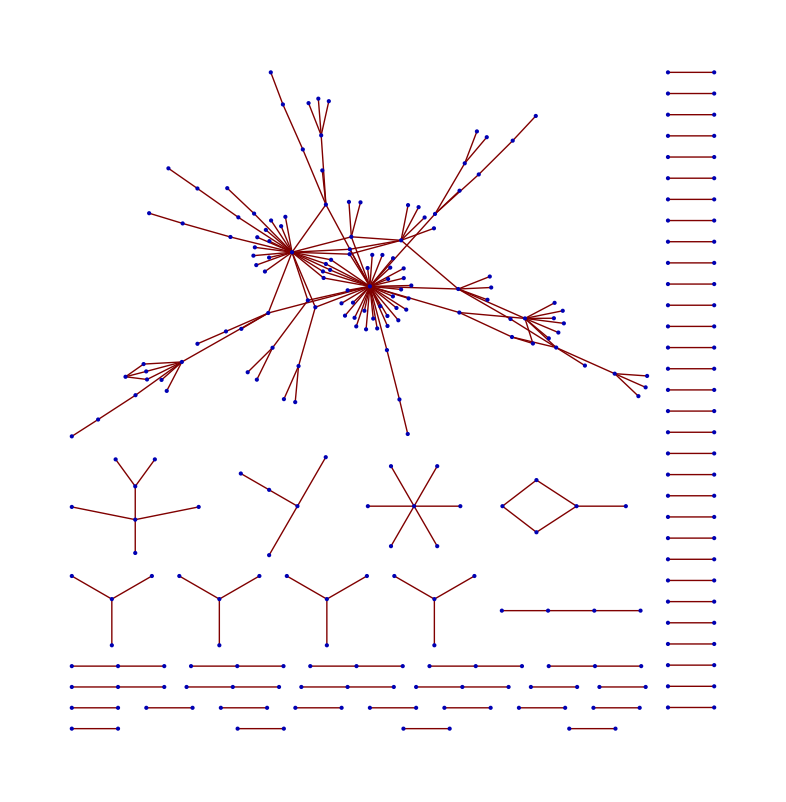

```mathematica
GraphPlot[split]
```